```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
dat=Import["infoseq_1000000_23.csv"]
```

{{9,8.99509×10^-6},{63,0.0000223753},{13,0.0000423247},{11,0.0000819628},{82,0.000152251},{83,0.000281068},{5,0.00047234},{1,0.000690619},{67,0.000820893},{53,0.000933726},{74,0.00103995},{16,0.00114339},{40,0.0012529},{54,0.00137422},{57,0.00154244},{51,0.00176335},{29,0.0020942},{66,0.00263217},{22,0.00342926},{70,0.00451066},{89,0.00582635},{77,0.00725472},{4,0.0086469}}

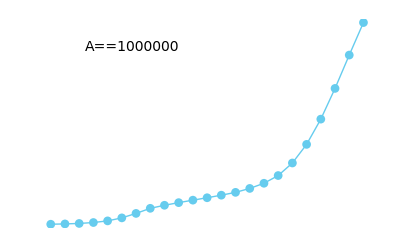

```mathematica
ListPlot[dat[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat],Style[#,12]&/@dat[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==10^6,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_A1000000",%]
```

progression_A1000000.pdf